27.9602

13.823

0.02

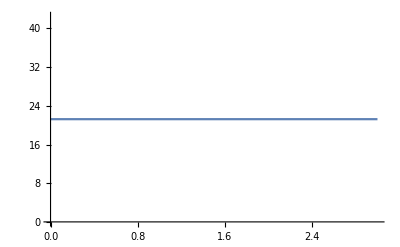

4.20973

-0.00150796

1.18305×10^-7

0.707107

General::munfl: -8.61573×10^-308 (-0.142045) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.16554×10^-308-8.61573×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -0.0236742 (-7.09918×10^-307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.{0.587145}

1.25{0.651876}

1.5{0.701325}

1.75{0.745122}

2.{0.783522}

2.25{0.821265}

2.5{0.848974}

2.75{0.869728}

3.{0.889233}

3.25{0.908748}

3.5{0.923882}

3.75{0.934854}

4.{0.945676}

4.25{0.953561}

4.5{0.961856}

4.75{0.96864}

5.{0.974514}

5.25{0.978093}

5.5{0.982181}

5.75{0.985019}

6.{0.987466}

6.25{0.989522}

6.5{0.991373}

6.75{0.992895}

7.{0.994062}

7.25{0.995181}

7.5{0.995997}

7.75{0.996706}

8.{0.997309}

8.25{0.99778}

8.5{0.998208}

8.75{0.998523}

9.{0.998787}

9.25{0.999014}

9.5{0.999201}

9.75{0.999353}

10.{0.999484}

10.25{0.99958}

10.5{0.999664}

10.75{0.999733}

11.{0.999783}

11.25{0.999828}

11.5{0.999864}

11.75{0.999893}

12.{0.999917}

12.25{0.999934}

12.5{0.999947}

12.75{0.999961}

13.{0.99997}

13.25{0.999977}

13.5{0.999983}

13.75{0.999988}

14.{0.999991}

14.25{0.999995}

14.5{0.999996}

14.75{0.999997}

15.{0.999998}

15.25{0.999999}

15.5{1.}

15.75{1.}

16.{1.}

16.25{1.}

16.5{1.}

16.75{1.}

17.{1.}

17.25{1.}

17.5{1.}

17.75{1.}

18.{1.}

18.25{1.}

18.5{1.}

18.75{1.}

19.{1.}

19.25{1.}

19.5{1.}

19.75{1.}

20.{1.}

20.25{1.}

20.5{1.}

20.75{1.}

21.{1.}

21.25{1.}

21.5{1.}

21.75{1.}

22.{1.}

22.25{1.}

22.5{1.}

22.75{1.}

23.{1.}

23.25{1.}

23.5{1.}

23.75{1.}

24.{1.}

24.25{1.}

24.5{1.}

24.75{1.}

25.{1.}

25.25{1.}

25.5{1.}

25.75{1.}

26.{1.}

26.25{1.}

26.5{1.}

26.75{1.}

27.{1.}

27.25{1.}

27.5{1.}

27.75{1.}

28.{1.}

28.25{1.}

28.5{1.}

28.75{1.}

29.{1.}

29.25{1.}

29.5{1.}

29.75{1.}

30.{1.}

30.25{1.}

30.5{1.}

30.75{1.}

31.{1.}

31.25{1.}

31.5{1.}

31.75{1.}

32.{1.}

32.25{1.}

32.5{1.}

32.75{1.}

33.{1.}

33.25{1.}

33.5{1.}

33.75{1.}

34.{1.}

34.25{1.}

34.5{1.}

34.75{1.}

35.{1.}

35.25{1.}

35.5{1.}

35.75{1.}

36.{1.}

36.25{1.}

36.5{1.}

36.75{1.}

37.{1.}

37.25{1.}

37.5{1.}

37.75{1.}

38.{1.}

38.25{1.}

38.5{1.}

38.75{1.}

39.{1.}

39.25{1.}

39.5{1.}

39.75{1.}

40.{1.}

40.25{1.}

40.5{1.}

40.75{1.}

41.{1.}

41.25{1.}

41.5{1.}

41.75{1.}

42.{1.}

42.25{1.}

42.5{1.}

42.75{1.}

43.{1.}

43.25{1.}

43.5{1.}

43.75{1.}

44.{1.}

44.25{1.}

44.5{1.}

44.75{1.}

45.{1.}

45.25{1.}

45.5{1.}

45.75{1.}

46.{1.}

46.25{1.}

46.5{1.}

46.75{1.}

47.{1.}

47.25{1.}

47.5{1.}

47.75{1.}

48.{1.}

48.25{1.}

48.5{1.}

48.75{1.}

49.{1.}

49.25{1.}

49.5{1.}

49.75{1.}

50.{1.}

```mathematica
kappa = (2 * Pi)* (4.44 +1*0.01)
gamma =(2 * Pi) * (2.30 -1*0.1)
T = 0.02(*temperature in Kelvin*)
aalpha[t_]:=(0.51-0.4*0.004) *(kappa + gamma)
Plot[aalpha[t], {t,0,3}]
Delta =(2 * Pi)* (0.70 -0.3* 0.10)
K = -(2 * Pi)* (0.0002 + 1* 0.00004)
nT = 0.5 * Coth[ 0.319/(2T)] - 0.5
sigmaSP = Sqrt[nT + 1/2]
(n =1-0.25;
Label[begin];
n=n+0.25;
b=1.1Sqrt[n];
U[Q_,t_] := (2/(aalpha[t] + (kappa + gamma)/2))* (0.25*( (kappa/2 + gamma/2)^2 + Delta^2 - aalpha[t]^2)* Q^2 + (3/2)* Delta *K* Q^4 + 3 K^2 Q^6) + Sqrt[2 kappa]* b *HeavisideTheta[t-0.228]*HeavisideTheta[1.228+0.04-t]*Q;
Diff = 0.5*(kappa + gamma)*(nT + 1/2);
(*Plot3D[U[Q,t], {Q, -15, 15}, {t,0,3}]*)
S=NDSolve[{D[W[Q,t],t] == D[W[Q,t],Q]*D[U[Q,t],Q] +W[Q,t]*D[U[Q,t],Q,Q]+ Diff * D[W[Q,t],Q,Q], W[Q,0] == (1/(Sqrt[2 Pi] sigmaSP)) Exp[-Q^2/(2 sigmaSP^2)], W[50,t]== 0, W[-50,t]== 0}, W, {Q,-50,50},{t,0,3}];
WW[Q_,t_] :=Evaluate[W[Q,t]/.S] ;
(*Plot3D[WW[Q,t],{Q,-25,25},{t,0,3},PlotRange->All]*)(*P[t_] := Integrate[WW[Q,t], {Q,-7.5,7.5}];*)
Pleft[t_] := Integrate[WW[Q,t], {Q,-50,-7.5}];
(*Pright[t_] := Integrate[WW[Q,t], {Q,7.5,50}];*)
(*Pdetected[t_] := 1 - P[t]*)
Print[n,Pleft[2]];
If[n<50,Goto[begin],Goto[end]];
                 Label[end]);
(*Plot[Pleft[t], {t,0,2},LabelStyle -> FontSize ->12]
Plot[Pright[t], {t,0,2},LabelStyle -> FontSize ->12]
Plot[Pdetected[t], {t,0,2},LabelStyle -> FontSize ->12]*)
(*Plot[(1-Exp[-0.76*nbar])*0.88 + 0.12, {nbar, 0.999, 1}, PlotRange->All]*)
(*Plot[(1-Exp[-(0.703^(1/(1 + 0.12 nbar)))*nbar])*0.744 + 0.256, {nbar, 3.999, 4}, PlotRange->All]*)
(*Plot[{P[t]/P[1.7],Exp[-1.1(t-0.15)]}, {t,0,4}]
Plot[-Log[P[t]]/(b^2 (t-1.2)), {t,0,4}] *)
 (* note from this plot that Pdark is around 2.5 for a 1 microsec pulse, which is what is observed experimentally*)
```